```mathematica
data={
{-Log[10,0.013602352551501930775],Log[10,3.6531533726327163899*10^26]},{-Log[10,0.011841535675862475616],Log[10,4.5187239139060929849*10^25]},{-Log[10,0.010308655552913227257],Log[10,6.4151689194034250436*10^23]},{-Log[10,0.0089742058984143262962],Log[10,1.0760158827750225347*10^21]},{-Log[10,0.0078124999999999895917],Log[10,56344952558728288]},{-Log[10,0.0068011762757509601832],Log[10,96393046911.700408936]},{-Log[10,0.005920767837931233471],Log[10,4065.4610565197490359]},{-Log[10,0.0051543277764566101593],Log[10,1.8666612192334339047*10^-7]},{-Log[10,0.0044871029492071596786],Log[10,7.8657435968598144058*10^-20]},{-Log[10,0.0039062499999999947958],Log[10,2.6908955483298965018*10^-36]},{-Log[10,0.0034005881378754826937],Log[10,3.3450140248436621717*10^-44]},{-Log[10,0.0029603839189656202049],Log[10,2.811780176591677157*10^-44]},{-Log[10,0.0025771638882283098501],Log[10,2.160887389108736528*10^-44]},{-Log[10,0.0022435514746035859109],Log[10,1.5744617784636914789*10^-44]},{-Log[10,0.0019531250000000026021],Log[10,1.0984202170640773287*10^-44]},{-Log[10,0.00170029406893774525],Log[10,7.4216042219953196139*10^-45]},{-Log[10,0.0014801919594828140056],Log[10,4.9669649408019095859*10^-45]},{-Log[10,0.0012885819441141579608],Log[10,3.2781876942335066565*10^-45]},{-Log[10,0.0011217757373017955575],Log[10,2.1597023833724270733*10^-45]},{-Log[10,0.00097656250000000368629],Log[10,1.4188217945082162436*10^-45]}}; (*亚当斯方法*)
data1={{-Log[10,0.023683071351724996334],Log[10,9934835247458222080]},{-Log[10,0.022097086912079635934],Log[10,7409286811606956032]},{-Log[10,0.020617311105826503087],Log[10,4000995602188158976]},{-Log[10,0.01923663145851434858],Log[10,1565002999513187840]},{-Log[10,0.017948411796828708104],Log[10,269182927929514624]},{-Log[10,0.016746460352129618337],Log[10,25327814374053624]},{-Log[10,0.015625000000000038164],Log[10,1246942487019686.25]},{-Log[10,0.014578640492762655681],Log[10,10261931818941.107422]},{-Log[10,0.013602352551501981082],Log[10,19862655432.053554535]},{-Log[10,0.012691443693066220902],Log[10,4127310.0916659370996]},{-Log[10,0.011841535675862525923],Log[10,0.024499620722879200674]},{-Log[10,0.011048543456039845723],Log[10,0.019153201834114508273]},{-Log[10,0.01030865555291327583],Log[10,0.017794300836518783804]},{-Log[10,0.0096183157292571985764],Log[10,0.01673399924092150437]},{-Log[10,0.0089742058984143766032],Log[10,0.015502329962158944987]},{-Log[10,0.0083732301760648299854],Log[10,0.014439389274800595864]},{-Log[10,0.0078125000000000381639],Log[10,0.013512747495219135097]},{-Log[10,0.0072893202463813460551],Log[10,0.012509165450684922583]},{-Log[10,0.0068011762757510061533],Log[10,0.011644261803080646622]},{-Log[10,0.0063457218465331269308],Log[10,0.01089116376248955298]},{-Log[10,0.0059207678379312777064],Log[10,0.010167745527614013845]},{-Log[10,0.0055242717280199367391],Log[10,0.0094276313015585477828]},{-Log[10,0.0051543277764566509253],Log[10,0.0087879160805951483937]},{-Log[10,0.0048091578646286114312],Log[10,0.0082294742583495228416]},{-Log[10,0.0044871029492071987099],Log[10,0.0076672630893960258547]},{-Log[10,0.0041866150880324254011],Log[10,0.0071464702100876298374]},{-Log[10,0.0039062500000000294903],Log[10,0.0066654140499593506064]},{-Log[10,0.0036446601231906821348],Log[10,0.0061990277527744774844]},{-Log[10,0.0034005881378755117503],Log[10,0.0057737572271227000087]},{-Log[10,0.003172860923266570838],Log[10,0.0053857938520314174724]},{-Log[10,0.0029603839189656457921],Log[10,0.0050315929650800450545]},{-Log[10,0.0027621358640099748748],Log[10,0.0046817050824613515303]},{-Log[10,0.0025771638882283319678],Log[10,0.0043659555187863796633]},{-Log[10,0.0024045789323143113535],Log[10,0.0040801867036178718351]},{-Log[10,0.0022435514746036049928],Log[10,0.0038035634665851691949]},{-Log[10,0.0020933075440162179047],Log[10,0.0035470506087129649586]},{-Log[10,0.0019531250000000195156],Log[10,0.0033098786711052152754]},{-Log[10,0.0018223300615953456211],Log[10,0.0030853718331881330172]},{-Log[10,0.0017002940689377599951],Log[10,0.002874580304626395133]},{-Log[10,0.0015864304616332893221],Log[10,0.0026821718770753122385]},{-Log[10,0.0014801919594828265823],Log[10,0.0025026894148550971053]},{-Log[10,0.0013810679320049909068],Log[10,0.0023327153520524834818]},{-Log[10,0.0012885819441141692365],Log[10,0.0021758882114010225095]},{-Log[10,0.0012022894661571587125],Log[10,0.0020314362416308240356]},{-Log[10,0.0011217757373018053153],Log[10,0.0018942489824138597498]},{-Log[10,0.0010466537720081113376],Log[10,0.0017669664734465406752]},{-Log[10,0.00097656250000001214306],Log[10,0.001649221961353974919]}};(*LMM1(a=b=c=0,Subscript[β, 0]=0.25)*)
data2={
{-Log[10,0.21763764082403105893],Log[10,65.59134217038739223]},{-Log[10,0.18946457081379977638],Log[10,59.11078923759183823]},{-Log[10,0.1649384888466117749],Log[10,29.040024186258399652]},{-Log[10,0.14358729437462933176],Log[10,29.040024186258399652]},{-Log[10,0.12499999999999997224],Log[10,0.08798096584339609727]},{-Log[10,0.10881882041201546008],Log[10,0.058657017445311682158]},{-Log[10,0.094732285406899818803],Log[10,0.12792923139699635682]},{-Log[10,0.082469244423305831937],Log[10,0.18964405599789532775]},{-Log[10,0.071793647187314638125],Log[10,0.18561176132168566433]},{-Log[10,0.062499999999999958367],Log[10,0.1205237387657687731]},{-Log[10,0.054409410206007723099],Log[10,0.09492792590279108822]},{-Log[10,0.047366142703449902462],Log[10,0.087557840089606375766]},{-Log[10,0.04123462221165290903],Log[10,0.079962446260277486587]},{-Log[10,0.035896823593657305185],Log[10,0.067933815131178854063]},{-Log[10,0.031249999999999958367],Log[10,0.056026608756375329001]},{-Log[10,0.027204705103003840733],Log[10,0.0502264000895240037]},{-Log[10,0.023683071351724933884],Log[10,0.04232279224891827285]},{-Log[10,0.020617311105826440637],Log[10,0.036853933073317912683]},{-Log[10,0.017948411796828638715],Log[10,0.031989737054830158502]},{-Log[10,0.015624999999999972244],Log[10,0.027316982841556536332]},{-Log[10,0.013602352551501911693],Log[10,0.023845529516511643209]},{-Log[10,0.011841535675862460003],Log[10,0.020634010675855962713]},{-Log[10,0.01030865555291321338],Log[10,0.017800669870966290276]},{-Log[10,0.0089742058984143158878],Log[10,0.015506740433289922798]},{-Log[10,0.007812499999999980918],Log[10,0.013408053812323794673]},{-Log[10,0.0068011762757509523769],Log[10,0.011646111053587704376]},{-Log[10,0.0059207678379312265321],Log[10,0.010168957994141414325]},{-Log[10,0.0051543277764566032204],Log[10,0.0087886853134178100078]},{-Log[10,0.0044871029492071544745],Log[10,0.0076677667402461624491]},{-Log[10,0.003906249999999990459],Log[10,0.0066394479821186846991]},{-Log[10,0.0034005881378754779232],Log[10,0.0057739673203281993707]},{-Log[10,0.0029603839189656167355],Log[10,0.0050317306819076534907]},{-Log[10,0.0025771638882283068143],Log[10,0.0043660446923254880858]},{-Log[10,0.0022435514746035828751],Log[10,0.0038036219729464804118]},{-Log[10,0.001953125],Log[10,0.0033034202565459525047]},{-Log[10,0.0017002940689377432984],Log[10,0.0028746052281913847537]},{-Log[10,0.0014801919594828122709],Log[10,0.0025027057734683388901]},{-Log[10,0.0012885819441141564429],Log[10,0.0021758989103494164041]},{-Log[10,0.0011217757373017942565],Log[10,0.0018942560123944574002]},{-Log[10,0.00097656250000000238524],Log[10,0.0016492265848797593719]}};(*XZ(γ=0.9,Subscript[β, 0]=0.01)*)
data3={{-Log[10,0.21763764082403105893],Log[10,77.278660037728386101]},{-Log[10,0.18946457081379977638],Log[10,77.938818893581895964]},{-Log[10,0.1649384888466117749],Log[10,45.993960489675139058]},{-Log[10,0.14358729437462933176],Log[10,45.993960489675139058]},{-Log[10,0.12499999999999997224],Log[10,0.86549355779282310941]},{-Log[10,0.10881882041201546008],Log[10,0.24895527990341090319]},{-Log[10,0.094732285406899818803],Log[10,0.22248252485952030311]},{-Log[10,0.082469244423305831937],Log[10,0.19325286846607420133]},{-Log[10,0.071793647187314638125],Log[10,0.17139572783086298724]},{-Log[10,0.062499999999999958367],Log[10,0.1148630830031343586]},{-Log[10,0.054409410206007723099],Log[10,0.09892431805843437953]},{-Log[10,0.047366142703449902462],Log[10,0.089341771018974724949]},{-Log[10,0.04123462221165290903],Log[10,0.07849586083897730493]},{-Log[10,0.035896823593657305185],Log[10,0.067561229980325876454]},{-Log[10,0.031249999999999958367],Log[10,0.056341708563812042954]},{-Log[10,0.027204705103003840733],Log[10,0.050080497436823245838]},{-Log[10,0.023683071351724933884],Log[10,0.04234971511106461195]},{-Log[10,0.020617311105826440637],Log[10,0.036861021658440129567]},{-Log[10,0.017948411796828638715],Log[10,0.031982558876112343604]},{-Log[10,0.015624999999999972244],Log[10,0.027318423229791000129]},{-Log[10,0.013602352551501911693],Log[10,0.023844767949491640913]},{-Log[10,0.011841535675862460003],Log[10,0.020633983059386296066]},{-Log[10,0.01030865555291321338],Log[10,0.01780060451419757106]},{-Log[10,0.0089742058984143158878],Log[10,0.015506684824021399471]},{-Log[10,0.007812499999999980918],Log[10,0.013408021844517947763]},{-Log[10,0.0068011762757509523769],Log[10,0.011646089686536131858]},{-Log[10,0.0059207678379312265321],Log[10,0.010168943952779452289]},{-Log[10,0.0051543277764566032204],Log[10,0.0087886764325543209608]},{-Log[10,0.0044871029492071544745],Log[10,0.0076677609400268575968]},{-Log[10,0.003906249999999990459],Log[10,0.0066394442677062404101]},{-Log[10,0.0034005881378754779232],Log[10,0.0057739649040088325549]},{-Log[10,0.0029603839189656167355],Log[10,0.0050317290984870366444]},{-Log[10,0.0025771638882283068143],Log[10,0.0043660436673653713058]},{-Log[10,0.0022435514746035828751],Log[10,0.0038036213007557329036]},{-Log[10,0.001953125],Log[10,0.003303419819343678121]},{-Log[10,0.0017002940689377432984],Log[10,0.0028746049418396646402]},{-Log[10,0.0014801919594828122709],Log[10,0.0025027055855308955046]},{-Log[10,0.0012885819441141564429],Log[10,0.0021758987879355595751]},{-Log[10,0.0011217757373017942565],Log[10,0.0018942559319139462559]},{-Log[10,0.00097656250000000238524],Log[10,0.0016492265313043930064]}};(*XZ(γ=0.9,Subscript[β, 0]=0)*)
data4={{-Log[10,0.10881882041201546008],Log[10,8210.9496669351538003]},{-Log[10,0.094732285406899818803],Log[10,7263.6024216928772148]},{-Log[10,0.082469244423305831937],Log[10,3146.3443447193963038]},{-Log[10,0.071793647187314638125],Log[10,1531.5433200129837132]},{-Log[10,0.062499999999999958367],Log[10,47.78347772666963067]},{-Log[10,0.054409410206007723099],Log[10,1.4340052490670349705]},{-Log[10,0.047366142703449902462],Log[10,0.088238503444922233854]},{-Log[10,0.04123462221165290903],Log[10,0.076817196168057988448]},{-Log[10,0.035896823593657305185],Log[10,0.067707675501114727989]},{-Log[10,0.031249999999999958367],Log[10,0.056493289505720023502]},{-Log[10,0.027204705103003840733],Log[10,0.049864059200972976615]},{-Log[10,0.023683071351724933884],Log[10,0.042385515081546309979]},{-Log[10,0.020617311105826440637],Log[10,0.036848478583215771298]},{-Log[10,0.017948411796828638715],Log[10,0.031969576385077858038]},{-Log[10,0.015624999999999972244],Log[10,0.027314741474299408797]},{-Log[10,0.013602352551501911693],Log[10,0.023840768799631872898]},{-Log[10,0.011841535675862460003],Log[10,0.020631796288330339628]},{-Log[10,0.01030865555291321338],Log[10,0.017799118329611229861]},{-Log[10,0.0089742058984143158878],Log[10,0.015505673998258751034]},{-Log[10,0.007812499999999980918],Log[10,0.013407366917774221626]},{-Log[10,0.0068011762757509523769],Log[10,0.011645662162069303491]},{-Log[10,0.0059207678379312265321],Log[10,0.010168663592011073504]},{-Log[10,0.0051543277764566032204],Log[10,0.0087884989675305336121]},{-Log[10,0.0044871029492071544745],Log[10,0.007667644966226627723]},{-Log[10,0.003906249999999990459],Log[10,0.0066393699813739326387]},{-Log[10,0.0034005881378754779232],Log[10,0.0057739165800544389739]},{-Log[10,0.0029603839189656167355],Log[10,0.0050316974287385463072]},{-Log[10,0.0025771638882283068143],Log[10,0.0043660231656919012977]},{-Log[10,0.0022435514746035828751],Log[10,0.003803607852829404834]},{-Log[10,0.001953125],Log[10,0.0033034110734536659137]},{-Log[10,0.0017002940689377432984],Log[10,0.0028745992154007860009]},{-Log[10,0.0014801919594828122709],Log[10,0.0025027018277838930516]},{-Log[10,0.0012885819441141564429],Log[10,0.0021758963302912492921]},{-Log[10,0.0011217757373017942565],Log[10,0.0018942543171083237041]},{-Log[10,0.00097656250000000238524],Log[10,0.0016492254706287345911]}};
(*XZ(γ=0.9,Subscript[β, 0]=-0.2)*)
data5={{-Log[10,0.3298769776932236053],Log[10,6.1899870752259342765]},{-Log[10,0.28717458874925877454],Log[10,6.1899870752259342765]},{-Log[10,0.25000000000000005551],Log[10,6.1899870752259342765]},{-Log[10,0.21763764082403105893],Log[10,4.6344053988730724569]},{-Log[10,0.18946457081379977638],Log[10,0.83070195811583857903]},{-Log[10,0.1649384888466117749],Log[10,0.54619510433618112533]},{-Log[10,0.14358729437462933176],Log[10,0.54619510433618112533]},{-Log[10,0.12499999999999997224],Log[10,0.26917129149995200343]},{-Log[10,0.10881882041201546008],Log[10,0.23739743323826331678]},{-Log[10,0.094732285406899818803],Log[10,0.21198132973307454163]},{-Log[10,0.082469244423305831937],Log[10,0.17393821768577630293]},{-Log[10,0.071793647187314638125],Log[10,0.15941772870852910504]},{-Log[10,0.062499999999999958367],Log[10,0.12716193131809316874]},{-Log[10,0.054409410206007723099],Log[10,0.11190403517608848993]},{-Log[10,0.047366142703449902462],Log[10,0.094737215443680300453]},{-Log[10,0.04123462221165290903],Log[10,0.082074869901350822055]},{-Log[10,0.035896823593657305185],Log[10,0.072361893593475001829]},{-Log[10,0.031249999999999958367],Log[10,0.060393104071691960932]},{-Log[10,0.027204705103003840733],Log[10,0.053304608219599314278]},{-Log[10,0.023683071351724933884],Log[10,0.045289554232762652131]},{-Log[10,0.020617311105826440637],Log[10,0.039341344810554734757]},{-Log[10,0.017948411796828638715],Log[10,0.034092641949257540546]},{-Log[10,0.015624999999999972244],Log[10,0.029083159559166071872]},{-Log[10,0.013602352551501911693],Log[10,0.025346035267292177373]},{-Log[10,0.011841535675862460003],Log[10,0.02189479611327582731]},{-Log[10,0.01030865555291321338],Log[10,0.018846509537201794338]},{-Log[10,0.0089742058984143158878],Log[10,0.016376268323675891025]},{-Log[10,0.007812499999999980918],Log[10,0.014116368529596634573]},{-Log[10,0.0068011762757509523769],Log[10,0.012222024758360650054]},{-Log[10,0.0059207678379312265321],Log[10,0.010637055154230523613]},{-Log[10,0.0051543277764566032204],Log[10,0.0091583479723066352207]},{-Log[10,0.0044871029492071544745],Log[10,0.0079597615596845860964]},{-Log[10,0.003906249999999990459],Log[10,0.0068637613495802218821]},{-Log[10,0.0034005881378754779232],Log[10,0.0059449856709311577063]},{-Log[10,0.0029603839189656167355],Log[10,0.0051602241126370573809]},{-Log[10,0.0025771638882283068143],Log[10,0.0044598180373258689002]},{-Log[10,0.0022435514746035828751],Log[10,0.003871297462730627359]},{-Log[10,0.001953125],Log[10,0.0033508382583722351455]},{-Log[10,0.0017002940689377432984],Log[10,0.0029072859500243186659]},{-Log[10,0.0014801919594828122709],Log[10,0.0025248071736345689686]},{-Log[10,0.0012885819441141564429],Log[10,0.0021905182302882630907]},{-Log[10,0.0011217757373017942565],Log[10,0.0019038234382520169419]},{-Log[10,0.00097656250000000238524],Log[10,0.0016554260130019482489]}};
(*XZ(γ=0.99,Subscript[β, 0]=-0.1)*)
data6={{-Log[10,0.3298769776932236053],Log[10,1.2908917348185664498]},{-Log[10,0.28717458874925877454],Log[10,1.2908917348185664498]},{-Log[10,0.25000000000000005551],Log[10,1.2908917348185664498]},{-Log[10,0.21763764082403105893],Log[10,1.0431965070027489073]},{-Log[10,0.18946457081379977638],Log[10,0.77907008299352653591]},{-Log[10,0.1649384888466117749],Log[10,0.57579487955943398081]},{-Log[10,0.14358729437462933176],Log[10,0.57579487955943398081]},{-Log[10,0.12499999999999997224],Log[10,0.32574342558779922907]},{-Log[10,0.10881882041201546008],Log[10,0.25278223913151981472]},{-Log[10,0.094732285406899818803],Log[10,0.20153749765351625101]},{-Log[10,0.082469244423305831937],Log[10,0.1406270964119436806]},{-Log[10,0.071793647187314638125],Log[10,0.12328758719816856892]},{-Log[10,0.062499999999999958367],Log[10,0.097706049643693893003]},{-Log[10,0.054409410206007723099],Log[10,0.091386815817702193865]},{-Log[10,0.047366142703449902462],Log[10,0.086927493278279033273]},{-Log[10,0.04123462221165290903],Log[10,0.083351407055219206566]},{-Log[10,0.035896823593657305185],Log[10,0.078762475774323936761]},{-Log[10,0.031249999999999958367],Log[10,0.068796037042054891675]},{-Log[10,0.027204705103003840733],Log[10,0.060056807666972578108]},{-Log[10,0.023683071351724933884],Log[10,0.048154466152343033958]},{-Log[10,0.020617311105826440637],Log[10,0.039179624353941844284]},{-Log[10,0.017948411796828638715],Log[10,0.032475320593073842002]},{-Log[10,0.015624999999999972244],Log[10,0.027896829579555970646]},{-Log[10,0.013602352551501911693],Log[10,0.025335646354207597142]},{-Log[10,0.011841535675862460003],Log[10,0.022711971054938662196]},{-Log[10,0.01030865555291321338],Log[10,0.019520890453068817649]},{-Log[10,0.0089742058984143158878],Log[10,0.016479900525475321693]},{-Log[10,0.007812499999999980918],Log[10,0.013941155024642548632]},{-Log[10,0.0068011762757509523769],Log[10,0.012218734831314859157]},{-Log[10,0.0059207678379312265321],Log[10,0.010788749654523477339]},{-Log[10,0.0051543277764566032204],Log[10,0.0092317078477500702505]},{-Log[10,0.0044871029492071544745],Log[10,0.0079516397625573054242]},{-Log[10,0.003906249999999990459],Log[10,0.0068860161763589777806]},{-Log[10,0.0034005881378754779232],Log[10,0.0059758522176047712549]},{-Log[10,0.0029603839189656167355],Log[10,0.0051687175541444974058]},{-Log[10,0.0025771638882283068143],Log[10,0.0044697534763002977343]},{-Log[10,0.0022435514746035828751],Log[10,0.0038796212207348190759]},{-Log[10,0.001953125],Log[10,0.0033553803742553123257]},{-Log[10,0.0017002940689377432984],Log[10,0.0029111045841061500283]},{-Log[10,0.0014801919594828122709],Log[10,0.0025271784281539755312]},{-Log[10,0.0012885819441141564429],Log[10,0.0021921738701676796168]},{-Log[10,0.0011217757373017942565],Log[10,0.0019048917343025273397]},{-Log[10,0.00097656250000000238524],Log[10,0.0016561244507123928926]}};
(*XZ(γ=0.99,Subscript[β, 0]=-0.001)*)
data7={{-Log[10,0.3298769776932236053],Log[10,1.2955561937909367831]},{-Log[10,0.28717458874925877454],Log[10,1.2955561937909367831]},{-Log[10,0.25000000000000005551],Log[10,1.2955561937909367831]},{-Log[10,0.21763764082403105893],Log[10,1.0612761274464177497]},{-Log[10,0.18946457081379977638],Log[10,0.79701582504477375135]},{-Log[10,0.1649384888466117749],Log[10,0.58975954897383153774]},{-Log[10,0.14358729437462933176],Log[10,0.58975954897383153774]},{-Log[10,0.12499999999999997224],Log[10,0.33169046138456803607]},{-Log[10,0.10881882041201546008],Log[10,0.25592058485010016344]},{-Log[10,0.094732285406899818803],Log[10,0.20265539381212149816]},{-Log[10,0.082469244423305831937],Log[10,0.13948591073319624445]},{-Log[10,0.071793647187314638125],Log[10,0.12163576772007819726]},{-Log[10,0.062499999999999958367],Log[10,0.09583808917744507383]},{-Log[10,0.054409410206007723099],Log[10,0.089888777658378382629]},{-Log[10,0.047366142703449902462],Log[10,0.086137378107378037573]},{-Log[10,0.04123462221165290903],Log[10,0.083157008908998075736]},{-Log[10,0.035896823593657305185],Log[10,0.078953291823062710098]},{-Log[10,0.031249999999999958367],Log[10,0.069215814291222699239]},{-Log[10,0.027204705103003840733],Log[10,0.060427833324674273818]},{-Log[10,0.023683071351724933884],Log[10,0.048320517615074387585]},{-Log[10,0.020617311105826440637],Log[10,0.039164428850364418899]},{-Log[10,0.017948411796828638715],Log[10,0.032365514996122113356]},{-Log[10,0.015624999999999972244],Log[10,0.02780878419722504491]},{-Log[10,0.013602352551501911693],Log[10,0.025320415906815108009]},{-Log[10,0.011841535675862460003],Log[10,0.022750895343565613604]},{-Log[10,0.01030865555291321338],Log[10,0.019554236600369589993]},{-Log[10,0.0089742058984143158878],Log[10,0.016480342836824313224]},{-Log[10,0.007812499999999980918],Log[10,0.013926381976931967444]},{-Log[10,0.0068011762757509523769],Log[10,0.01221568077634216376]},{-Log[10,0.0059207678379312265321],Log[10,0.01079540271052681355]},{-Log[10,0.0051543277764566032204],Log[10,0.009233784608851158815]},{-Log[10,0.0044871029492071544745],Log[10,0.0079495382403316217079]},{-Log[10,0.003906249999999990459],Log[10,0.0068863431957917331516]},{-Log[10,0.0034005881378754779232],Log[10,0.0059767684439181456568]},{-Log[10,0.0029603839189656167355],Log[10,0.0051685226023742147916]},{-Log[10,0.0025771638882283068143],Log[10,0.0044698949603729776214]},{-Log[10,0.0022435514746035828751],Log[10,0.0038797509744138425347]},{-Log[10,0.001953125],Log[10,0.0033554045183595837543]},{-Log[10,0.0017002940689377432984],Log[10,0.0029111584314942540175]},{-Log[10,0.0014801919594828122709],Log[10,0.0025272008668503209705]},{-Log[10,0.0012885819441141564429],Log[10,0.0021921932906939778363]},{-Log[10,0.0011217757373017942565],Log[10,0.0019049033628955047703]},{-Log[10,0.00097656250000000238524],Log[10,0.0016561322791561750023]}};
(*XZ(γ=0.99,Subscript[β, 0]=0.0001)*)
data8={{-Log[10,0.5],Log[10,0.018628337791278148927]},{-Log[10,0.43527528164806211786],Log[10,0.018628337791278148927]},{-Log[10,0.37892914162759955277],Log[10,0.018628337791278148927]},{-Log[10,0.3298769776932236053],Log[10,0.018492968907065199247]},{-Log[10,0.28717458874925877454],Log[10,0.018492968907065199247]},{-Log[10,0.25000000000000005551],Log[10,0.018492968907065199247]},{-Log[10,0.21763764082403105893],Log[10,0.019059735675443056913]},{-Log[10,0.18946457081379977638],Log[10,0.019519424018197728543]},{-Log[10,0.1649384888466117749],Log[10,0.019492307787831397725]},{-Log[10,0.14358729437462933176],Log[10,0.019492307787831397725]},{-Log[10,0.12499999999999997224],Log[10,0.017307386668572011246]},{-Log[10,0.10881882041201546008],Log[10,0.01523641188921531775]},{-Log[10,0.094732285406899818803],Log[10,0.01277296898700608363]},{-Log[10,0.082469244423305831937],Log[10,0.0077051902446835240923]},{-Log[10,0.071793647187314638125],Log[10,0.0055356166485704960678]},{-Log[10,0.062499999999999958367],Log[10,0.0014969533350840391606]},{-Log[10,0.054409410206007723099],Log[10,0.00048084505534051746878]},{-Log[10,0.047366142703449902462],Log[10,5.9019969910423242254*10^-5]},{-Log[10,0.04123462221165290903],Log[10,4.560580830537119823*10^-6]},{-Log[10,0.035896823593657305185],Log[10,2.0876954942572467644*10^-7]},{-Log[10,0.031249999999999958367],Log[10,7.6216661870631696729*10^-9]},{-Log[10,0.027204705103003840733],Log[10,4.9773392074570210752*10^-9]},{-Log[10,0.023683071351724933884],Log[10,3.1265396938096046142*10^-9]},{-Log[10,0.020617311105826440637],Log[10,2.0911237186282960465*10^-9]},{-Log[10,0.017948411796828638715],Log[10,1.3879787319481806662*10^-9]},{-Log[10,0.015624999999999972244],Log[10,8.796695594170955701*10^-10]},{-Log[10,0.013602352551501911693],Log[10,5.9214511072269715442*10^-10]},{-Log[10,0.011841535675862460003],Log[10,3.8826741821651467035*10^-10]},{-Log[10,0.01030865555291321338],Log[10,2.5192470332058292115*10^-10]},{-Log[10,0.0089742058984143158878],Log[10,1.6799595048411219977*10^-10]},{-Log[10,0.007812499999999980918],Log[10,1.094844215288048872*10^-10]},{-Log[10,0.0068011762757509523769],Log[10,7.2240879944729385898*10^-11]},{-Log[10,0.0059207678379312265321],Log[10,4.8375414785084558389*10^-11]},{-Log[10,0.0051543277764566032204],Log[10,3.1402658251522552746*10^-11]},{-Log[10,0.0044871029492071544745],Log[10,2.0950796653096404043*10^-11]},{-Log[10,0.003906249999999990459],Log[10,1.3655743202889425447*10^-11]},{-Log[10,0.0034005881378754779232],Log[10,9.0123464246971707325*10^-12]},{-Log[10,0.0029603839189656167355],Log[10,5.9848792588468313625*10^-12]},{-Log[10,0.0025771638882283068143],Log[10,3.9217518121859029634*10^-12]},{-Log[10,0.0022435514746035828751],Log[10,2.6014745913016668055*10^-12]},{-Log[10,0.001953125],Log[10,1.7051915435217779304*10^-12]},{-Log[10,0.0017002940689377432984],Log[10,1.1378675779383229383*10^-12]},{-Log[10,0.0014801919594828122709],Log[10,7.3252515164767828537*10^-13]},{-Log[10,0.0012885819441141564429],Log[10,4.9216186681633189437*10^-13]},{-Log[10,0.0011217757373017942565],Log[10,3.2762681456688369508*10^-13]},{-Log[10,0.00097656250000000238524],Log[10,2.1360690993788011838*10^-13]}};
(*AM3(α=1)*)
data9={{-Log[10,0.5],Log[10,0.0099086313509560985935]},{-Log[10,0.43527528164806211786],Log[10,0.0099086313509560985935]},{-Log[10,0.37892914162759955277],Log[10,0.0099086313509560985935]},{-Log[10,0.3298769776932236053],Log[10,0.0059044409986380719246]},{-Log[10,0.28717458874925877454],Log[10,0.0059044409986380719246]},{-Log[10,0.25000000000000005551],Log[10,0.0059044409986380719246]},{-Log[10,0.21763764082403105893],Log[10,0.0037658854024928967164]},{-Log[10,0.18946457081379977638],Log[10,0.0022828794399654128711]},{-Log[10,0.1649384888466117749],Log[10,0.0013717219769724398049]},{-Log[10,0.14358729437462933176],Log[10,0.0013717219769724398049]},{-Log[10,0.12499999999999997224],Log[10,0.00040808239858680650514]},{-Log[10,0.10881882041201546008],Log[10,0.00019499593168037510083]},{-Log[10,0.094732285406899818803],Log[10,9.4428384436739953856*10^-5]},{-Log[10,0.082469244423305831937],Log[10,1.7183042752444421808*10^-5]},{-Log[10,0.071793647187314638125],Log[10,4.3206464993561510823*10^-6]},{-Log[10,0.062499999999999958367],Log[10,8.6924207864935709722*10^-7]},{-Log[10,0.054409410206007723099],Log[10,4.9318834061118366208*10^-7]},{-Log[10,0.047366142703449902462],Log[10,2.9389113265221311622*10^-7]},{-Log[10,0.04123462221165290903],Log[10,1.9075980095539790682*10^-7]},{-Log[10,0.035896823593657305185],Log[10,1.3035841739394982142*10^-7]},{-Log[10,0.031249999999999958367],Log[10,7.5581890968123843777*10^-8]},{-Log[10,0.027204705103003840733],Log[10,5.1990058591577792413*10^-8]},{-Log[10,0.023683071351724933884],Log[10,3.2000954330868580655*10^-8]},{-Log[10,0.020617311105826440637],Log[10,2.1087111057305207851*10^-8]},{-Log[10,0.017948411796828638715],Log[10,1.3814770327691405782*10^-8]},{-Log[10,0.015624999999999972244],Log[10,8.6447686786783606294*10^-9]},{-Log[10,0.013602352551501911693],Log[10,5.7623824600838702281*10^-9]},{-Log[10,0.011841535675862460003],Log[10,3.7431170385460177386*10^-9]},{-Log[10,0.01030865555291321338],Log[10,2.4080354377176149683*10^-9]},{-Log[10,0.0089742058984143158878],Log[10,1.594435694585172314*10^-9]},{-Log[10,0.007812499999999980918],Log[10,1.0321993260120621017*10^-9]},{-Log[10,0.0068011762757509523769],Log[10,6.7719696517087868415*10^-10]},{-Log[10,0.0059207678379312265321],Log[10,4.5125125858191950101*10^-10]},{-Log[10,0.0051543277764566032204],Log[10,2.9156710379396599819*10^-10]},{-Log[10,0.0044871029492071544745],Log[10,1.9376633630940887087*10^-10]},{-Log[10,0.003906249999999990459],Log[10,1.2587186848378451032*10^-10]},{-Log[10,0.0034005881378754779232],Log[10,8.2826634439925328479*10^-11]},{-Log[10,0.0029603839189656167355],Log[10,5.4840354479779307439*10^-11]},{-Log[10,0.0025771638882283068143],Log[10,3.5842329104696091235*10^-11]},{-Log[10,0.0022435514746035828751],Log[10,2.3707924512450517796*10^-11]},{-Log[10,0.001953125],Log[10,1.5532464203715790063*10^-11]},{-Log[10,0.0017002940689377432984],Log[10,1.0250467141759145306*10^-11]},{-Log[10,0.0014801919594828122709],Log[10,6.7474914544618513901*10^-12]},{-Log[10,0.0012885819441141564429],Log[10,4.4444448121794266626*10^-12]},{-Log[10,0.0011217757373017942565],Log[10,2.9327651418498135172*10^-12]},{-Log[10,0.00097656250000000238524],Log[10,1.9350077096191853343*10^-12]}};
(*AM3(α=1.8)*)
data10={{-Log[10,0.5],Log[10,0.0088237381034914630362]},{-Log[10,0.43527528164806211786],Log[10,0.0088237381034914630362]},{-Log[10,0.37892914162759955277],Log[10,0.0088237381034914630362]},{-Log[10,0.3298769776932236053],Log[10,0.0048713085329519234534]},{-Log[10,0.28717458874925877454],Log[10,0.0048713085329519234534]},{-Log[10,0.25000000000000005551],Log[10,0.0048713085329519234534]},{-Log[10,0.21763764082403105893],Log[10,0.0029156441051738646308]},{-Log[10,0.18946457081379977638],Log[10,0.0016246185849829730685]},{-Log[10,0.1649384888466117749],Log[10,0.00092297843605271268075]},{-Log[10,0.14358729437462933176],Log[10,0.00092297843605271268075]},{-Log[10,0.12499999999999997224],Log[10,0.00024036499694946034111]},{-Log[10,0.10881882041201546008],Log[10,9.7697264870966193939*10^-5]},{-Log[10,0.094732285406899818803],Log[10,5.1033153419477450541*10^-5]},{-Log[10,0.082469244423305831937],Log[10,1.0750719063090663496*10^-5]},{-Log[10,0.071793647187314638125],Log[10,1.5370840235062743773*10^-6]},{-Log[10,0.062499999999999958367],Log[10,2.4650790385605247934*10^-6]},{-Log[10,0.054409410206007723099],Log[10,1.9003678324303052705*10^-6]},{-Log[10,0.047366142703449902462],Log[10,1.3794575011161214206*10^-6]},{-Log[10,0.04123462221165290903],Log[10,1.0436378141687185916*10^-6]},{-Log[10,0.035896823593657305185],Log[10,8.1423366771193883551*10^-7]},{-Log[10,0.031249999999999958367],Log[10,5.6699104455937288094*10^-7]},{-Log[10,0.027204705103003840733],Log[10,4.3989084341777839882*10^-7]},{-Log[10,0.023683071351724933884],Log[10,3.1429082092415683292*10^-7]},{-Log[10,0.020617311105826440637],Log[10,2.3392733583538216635*10^-7]},{-Log[10,0.017948411796828638715],Log[10,1.7236681026933098337*10^-7]},{-Log[10,0.015624999999999972244],Log[10,1.2199043353255945021*10^-7]},{-Log[10,0.013602352551501911693],Log[10,8.987395871962178262*10^-8]},{-Log[10,0.011841535675862460003],Log[10,6.4479419248364422401*10^-8]},{-Log[10,0.01030865555291321338],Log[10,4.5544100379935059664*10^-8]},{-Log[10,0.0089742058984143158878],Log[10,3.2644329572839581033*10^-8]},{-Log[10,0.007812499999999980918],Log[10,2.2768804730510794343*10^-8]},{-Log[10,0.0068011762757509523769],Log[10,1.590634735038065628*10^-8]},{-Log[10,0.0059207678379312265321],Log[10,1.1156493173736237168*10^-8]},{-Log[10,0.0051543277764566032204],Log[10,7.5376843655661218691*10^-9]},{-Log[10,0.0044871029492071544745],Log[10,5.1710697945850370161*10^-9]},{-Log[10,0.003906249999999990459],Log[10,3.4381862912269411936*10^-9]},{-Log[10,0.0034005881378754779232],Log[10,2.2917857611659542272*10^-9]},{-Log[10,0.0029603839189656167355],Log[10,1.5237751060936943759*10^-9]},{-Log[10,0.0025771638882283068143],Log[10,9.9266872499725877788*10^-10]},{-Log[10,0.0022435514746035828751],Log[10,6.5065730581181924208*10^-10]},{-Log[10,0.001953125],Log[10,4.2068193373268059077*10^-10]},{-Log[10,0.0017002940689377432984],Log[10,2.7289970283561615361*10^-10]},{-Log[10,0.0014801919594828122709],Log[10,1.7712198374653098654*10^-10]},{-Log[10,0.0012885819441141564429],Log[10,1.1452927495270159852*10^-10]},{-Log[10,0.0011217757373017942565],Log[10,7.43785033563426623*10^-11]},{-Log[10,0.00097656250000000238524],Log[10,4.8277049025102769519*10^-11]}};
(*AM3(α=1.8)*)
data11={{-Log[10,0.21763764082403105893],Log[10,63.036300550822126354]},{-Log[10,0.18946457081379977638],Log[10,55.196068043491187893]},{-Log[10,0.1649384888466117749],Log[10,25.794293712304742883]},{-Log[10,0.14358729437462933176],Log[10,25.794293712304742883]},{-Log[10,0.12499999999999997224],Log[10,0.12433421645869874306]},{-Log[10,0.10881882041201546008],Log[10,0.029050224299491861357]},{-Log[10,0.094732285406899818803],Log[10,0.10210941657304645203]},{-Log[10,0.082469244423305831937],Log[10,0.18408107266485454478]},{-Log[10,0.071793647187314638125],Log[10,0.18718619445487372221]},{-Log[10,0.062499999999999958367],Log[10,0.12304881472269202369]},{-Log[10,0.054409410206007723099],Log[10,0.094100383800994613637]},{-Log[10,0.047366142703449902462],Log[10,0.086808530440589837252]},{-Log[10,0.04123462221165290903],Log[10,0.080381234135312673583]},{-Log[10,0.035896823593657305185],Log[10,0.068103833214582742972]},{-Log[10,0.031249999999999958367],Log[10,0.055913566266919123571]},{-Log[10,0.027204705103003840733],Log[10,0.050269036720641424587]},{-Log[10,0.023683071351724933884],Log[10,0.042316198606448973685]},{-Log[10,0.020617311105826440637],Log[10,0.036850656626548294881]},{-Log[10,0.017948411796828638715],Log[10,0.031992299154105729997]},{-Log[10,0.015624999999999972244],Log[10,0.027316428557570771041]},{-Log[10,0.013602352551501911693],Log[10,0.023845776110385741298]},{-Log[10,0.011841535675862460003],Log[10,0.020634006997118370386]},{-Log[10,0.01030865555291321338],Log[10,0.017800683955681018134]},{-Log[10,0.0089742058984143158878],Log[10,0.015506753947619689171]},{-Log[10,0.007812499999999980918],Log[10,0.013408061142606619853]},{-Log[10,0.0068011762757509523769],Log[10,0.011646116002589801397]},{-Log[10,0.0059207678379312265321],Log[10,0.010168961249928942792]},{-Log[10,0.0051543277764566032204],Log[10,0.0087886873720446345715]},{-Log[10,0.0044871029492071544745],Log[10,0.007667768084730242073]},{-Log[10,0.003906249999999990459],Log[10,0.0066394488430020492942]},{-Log[10,0.0034005881378754779232],Log[10,0.0057739678802015692582]},{-Log[10,0.0029603839189656167355],Log[10,0.0050317310488132704904]},{-Log[10,0.0025771638882283068143],Log[10,0.004366044930109391764]},{-Log[10,0.0022435514746035828751],Log[10,0.0038036221289032834392]},{-Log[10,0.001953125],Log[10,0.0033034203578541365687]},{-Log[10,0.0017002940689377432984],Log[10,0.0028746052943152688997]},{-Log[10,0.0014801919594828122709],Log[10,0.0025027058171251947982]},{-Log[10,0.0012885819441141564429],Log[10,0.0021758989388185323577]},{-Log[10,0.0011217757373017942565],Log[10,0.0018942560312551481871]},{-Log[10,0.00097656250000000238524],Log[10,0.001649226596753483598]}};
(*XZ(γ=0.9,Subscript[β, 0]=0.012318)*)
data12={{-Log[10,0.3298769776932236053],Log[10,1.2957171458445984058]},{-Log[10,0.28717458874925877454],Log[10,1.2957171458445984058]},{-Log[10,0.25000000000000005551],Log[10,1.2957171458445984058]},{-Log[10,0.21763764082403105893],Log[10,1.0620375716389356402]},{-Log[10,0.18946457081379977638],Log[10,0.79778849935691986683]},{-Log[10,0.1649384888466117749],Log[10,0.59036788500919679112]},{-Log[10,0.14358729437462933176],Log[10,0.59036788500919679112]},{-Log[10,0.12499999999999997224],Log[10,0.33195423440301147222]},{-Log[10,0.10881882041201546008],Log[10,0.25606166392196344495]},{-Log[10,0.094732285406899818803],Log[10,0.20270761181118873706]},{-Log[10,0.082469244423305831937],Log[10,0.13943787361003837089]},{-Log[10,0.071793647187314638125],Log[10,0.12156474197933239689]},{-Log[10,0.062499999999999958367],Log[10,0.095756331943641914695]},{-Log[10,0.054409410206007723099],Log[10,0.0898228391504496404]},{-Log[10,0.047366142703449902462],Log[10,0.086102292824373038993]},{-Log[10,0.04123462221165290903],Log[10,0.083148105591764109867]},{-Log[10,0.035896823593657305185],Log[10,0.078961417333687278219]},{-Log[10,0.031249999999999958367],Log[10,0.069234180351327834213]},{-Log[10,0.027204705103003840733],Log[10,0.060444145053194175965]},{-Log[10,0.023683071351724933884],Log[10,0.048327864209466997458]},{-Log[10,0.020617311105826440637],Log[10,0.039163796250623328365]},{-Log[10,0.017948411796828638715],Log[10,0.032360694597124761707]},{-Log[10,0.015624999999999972244],Log[10,0.027804900141464305996]},{-Log[10,0.013602352551501911693],Log[10,0.025319733018389134482]},{-Log[10,0.011841535675862460003],Log[10,0.022752601781913905921]},{-Log[10,0.01030865555291321338],Log[10,0.019555703005504243563]},{-Log[10,0.0089742058984143158878],Log[10,0.016480361922743491654]},{-Log[10,0.007812499999999980918],Log[10,0.013925730731368046733]},{-Log[10,0.0068011762757509523769],Log[10,0.012215545464448474]},{-Log[10,0.0059207678379312265321],Log[10,0.010795694815260103994]},{-Log[10,0.0051543277764566032204],Log[10,0.009233875219661791256]},{-Log[10,0.0044871029492071544745],Log[10,0.0079494452750774602379]},{-Log[10,0.003906249999999990459],Log[10,0.0068863573548676448866]},{-Log[10,0.0034005881378754779232],Log[10,0.0059768083879438993478]},{-Log[10,0.0029603839189656167355],Log[10,0.0051685137272877712533]},{-Log[10,0.0025771638882283068143],Log[10,0.0044699010155324625515]},{-Log[10,0.0022435514746035828751],Log[10,0.0038797566357556823036]},{-Log[10,0.001953125],Log[10,0.0033554055287547956965]},{-Log[10,0.0017002940689377432984],Log[10,0.0029111606962679559274]},{-Log[10,0.0014801919594828122709],Log[10,0.0025272019235602627418]},{-Log[10,0.0012885819441141564429],Log[10,0.0021921941427922586598]},{-Log[10,0.0011217757373017942565],Log[10,0.0019049037674350177696]},{-Log[10,0.00097656250000000238524],Log[10,0.001656132768291018742]}};
(*XZ(γ=0.99,Subscript[β, 0]=0.000147)*)
data13={{-Log[10,0.5],Log[10,0.92777425177251460209]},{-Log[10,0.43527528164806211786],Log[10,0.92777425177251460209]},{-Log[10,0.37892914162759955277],Log[10,0.92777425177251460209]},{-Log[10,0.3298769776932236053],Log[10,1.2952032861088353943]},{-Log[10,0.28717458874925877454],Log[10,1.2952032861088353943]},{-Log[10,0.25000000000000005551],Log[10,1.2952032861088353943]},{-Log[10,0.21763764082403105893],Log[10,1.0596529133516106036]},{-Log[10,0.18946457081379977638],Log[10,0.79537338367769694347]},{-Log[10,0.1649384888466117749],Log[10,0.58846838768057163627]},{-Log[10,0.14358729437462933176],Log[10,0.58846838768057163627]},{-Log[10,0.12499999999999997224],Log[10,0.33113191309204537127]},{-Log[10,0.10881882041201546008],Log[10,0.25562235577522651742]},{-Log[10,0.094732285406899818803],Log[10,0.20254553526952892573]},{-Log[10,0.082469244423305831937],Log[10,0.13958832924287689625]},{-Log[10,0.071793647187314638125],Log[10,0.12178677243646568451]},{-Log[10,0.062499999999999958367],Log[10,0.096011506449440453537]},{-Log[10,0.054409410206007723099],Log[10,0.090028538652374978657]},{-Log[10,0.047366142703449902462],Log[10,0.086211659268571771975]},{-Log[10,0.04123462221165290903],Log[10,0.083175784930139273765]},{-Log[10,0.035896823593657305185],Log[10,0.078935994339646042839]},{-Log[10,0.031249999999999958367],Log[10,0.069176856105106765416]},{-Log[10,0.027204705103003840733],Log[10,0.060393254587368327968]},{-Log[10,0.023683071351724933884],Log[10,0.048304956611054328253]},{-Log[10,0.020617311105826440637],Log[10,0.03916577971566809202]},{-Log[10,0.017948411796828638715],Log[10,0.03237573561439593961]},{-Log[10,0.015624999999999972244],Log[10,0.027817014257388139598]},{-Log[10,0.013602352551501911693],Log[10,0.025321859896891563135]},{-Log[10,0.011841535675862460003],Log[10,0.022747276612704148135]},{-Log[10,0.01030865555291321338],Log[10,0.01955112816425275124]},{-Log[10,0.0089742058984143158878],Log[10,0.016480302310482475292]},{-Log[10,0.007812499999999980918],Log[10,0.013927762073360105965]},{-Log[10,0.0068011762757509523769],Log[10,0.012215967403500616051]},{-Log[10,0.0059207678379312265321],Log[10,0.010794783402277130513]},{-Log[10,0.0051543277764566032204],Log[10,0.0092335923701585276291]},{-Log[10,0.0044871029492071544745],Log[10,0.0079497351858544007541]},{-Log[10,0.003906249999999990459],Log[10,0.0068863130472995859321]},{-Log[10,0.0034005881378754779232],Log[10,0.0059766835003677298843]},{-Log[10,0.0029603839189656167355],Log[10,0.005168541144567440071]},{-Log[10,0.0025771638882283068143],Log[10,0.0044698819181457905003]},{-Log[10,0.0022435514746035828751],Log[10,0.0038797390390543640137]},{-Log[10,0.001953125],Log[10,0.0033554023358813855893]},{-Log[10,0.0017002940689377432984],Log[10,0.0029111533543206835617]},{-Log[10,0.0014801919594828122709],Log[10,0.0025271986757323672279]},{-Log[10,0.0012885819441141564429],Log[10,0.002192191610007276914]},{-Log[10,0.0011217757373017942565],Log[10,0.0019049022799657588934]},{-Log[10,0.00097656250000000238524],Log[10,0.0016561318716504791482]}};
(*XZ(γ=0.99,Subscript[β, 0]=0)*)
```

OptionValue::nodef: Graphics 的未知选项 Image.

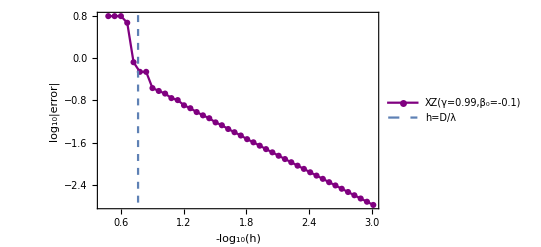

OptionValue::nodef: Graphics 的未知选项 Image.

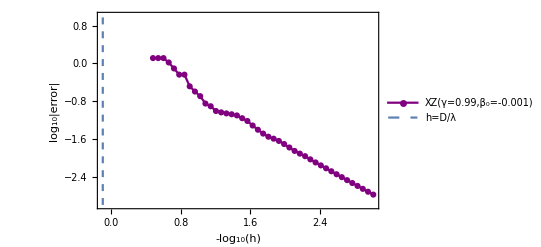

OptionValue::nodef: Graphics 的未知选项 Image.

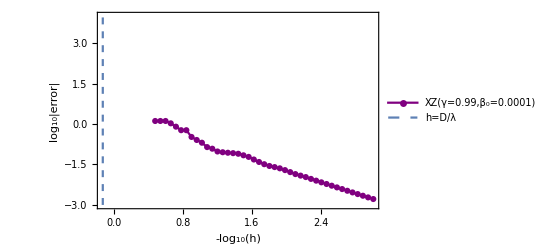

OptionValue::nodef: Graphics 的未知选项 Image.

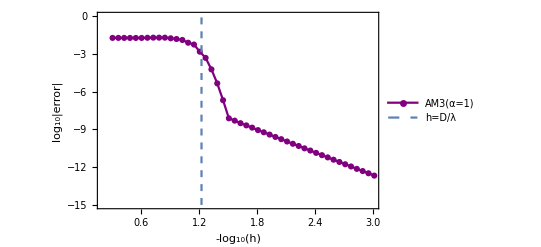

OptionValue::nodef: Graphics 的未知选项 Image.

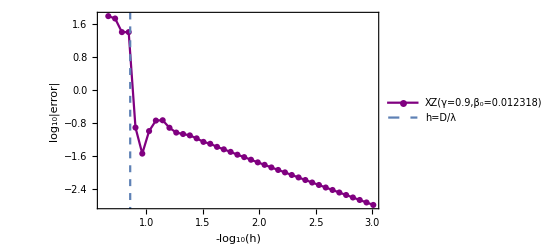

OptionValue::nodef: Graphics 的未知选项 Image.

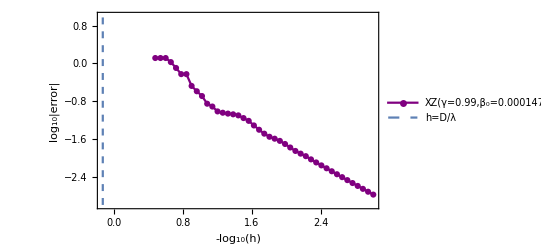

OptionValue::nodef: Graphics 的未知选项 Image.

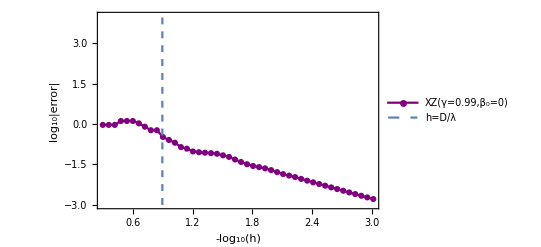

```mathematica
p1=ListLinePlot[data,Joined->True,PlotStyle->Purple,PlotLegends->{"Explicit_Adams3"},PlotMarkers->Automatic];
Show[p1,ParametricPlot[{-Log[10,6/1100],t},{t,-50,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "}];
p2=ListLinePlot[data1,Joined->True,PlotStyle->Purple,PlotLegends->{"XZ(γ=0,β_0=0.25)"},PlotMarkers->Automatic];
Show[p2,ParametricPlot[{-Log[10,6/500],t},{t,-50,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "}];
p3=ListLinePlot[data2,Joined->True,PlotStyle->Purple,PlotLegends->{"XZ(γ=0.9,β_0=0.01)"},PlotRange->Full,PlotMarkers->Automatic];
Show[p3,ParametricPlot[{-Log[10,41154/301100],t},{t,-3,4},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "}];
p4=ListLinePlot[data3,Joined->True,PlotStyle->Purple,PlotLegends->{"XZ(γ=0.9,β_0=0)"},PlotRange->Full,PlotMarkers->Automatic];
Show[p4,ParametricPlot[{-Log[10,41154/325100],t},{t,-3,4},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "}];
p5=ListLinePlot[data4,Joined->True,PlotStyle->Purple,PlotLegends->{"XZ(γ=0.9,β_0=-0.2)"},PlotRange->Full,PlotMarkers->Automatic];
Show[p5,ParametricPlot[{-Log[10,41154/805100],t},{t,-3,4},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "}];
p6=ListLinePlot[data5,Joined->True,PlotStyle->Purple,PlotLegends->{"XZ(γ=0.99,β_0=-0.1)"},PlotRange->Full,PlotMarkers->Automatic];
Show[p6,ParametricPlot[{-Log[10,0.17154],t},{t,-3,4},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "}]
p7=ListLinePlot[data6,Joined->True,PlotStyle->Purple,PlotLegends->{"XZ(γ=0.99,β_0=-0.001)"},PlotMarkers->Automatic];
Show[p7,ParametricPlot[{-Log[10,1.242960745],t},{t,-3,1},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "},PlotRange->Full]
p8=ListLinePlot[data7,Joined->True,PlotStyle->Purple,PlotLegends->{"XZ(γ=0.99,β_0=0.0001)"},PlotRange->Full,PlotMarkers->Automatic];
Show[p8,ParametricPlot[{-Log[10,1.33565324],t},{t,-3,4},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "},PlotRange->Full]
p9=ListLinePlot[data8,Joined->True,PlotStyle->Purple,PlotLegends->{"AM3(α=1)"},PlotRange->Full,PlotMarkers->Automatic];
Show[p9,ParametricPlot[{-Log[10,0.06],t},{t,-15,0},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "},PlotRange->{{0.2,3},{-15,0}}]
p10=ListLinePlot[data9,Joined->True,PlotStyle->Purple,PlotLegends->{"AM3(α=1.8)"},PlotRange->Full,PlotMarkers->Automatic];
Show[p10,ParametricPlot[{-Log[10,0.54],t},{t,-15,0},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "},PlotRange->Full];
p11=ListLinePlot[data10,Joined->True,PlotStyle->Purple,PlotLegends->{"AM3(α=1.99)"},PlotMarkers->Automatic];
Show[p11,ParametricPlot[{-Log[10,11.94],t},{t,-11,0},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "},PlotRange->Full];
p12=ListLinePlot[data11,Joined->True,PlotStyle->Purple,PlotLegends->{"XZ(γ=0.9,β_0=0.012318)"},PlotRange->Full,PlotMarkers->Automatic];
Show[p12,ParametricPlot[{-Log[10,0.13925],t},{t,-3,4},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "}]
p13=ListLinePlot[data12,Joined->True,PlotStyle->Purple,PlotLegends->{"XZ(γ=0.99,β_0=0.000147)"},PlotMarkers->Automatic];
Show[p13,ParametricPlot[{-Log[10,1.33992585],t},{t,-3,1},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "},PlotRange->Full]
p14=ListLinePlot[data13,Joined->True,PlotStyle->Purple,PlotLegends->{"XZ(γ=0.99,β_0=0)"},PlotRange->Full,PlotMarkers->Automatic];
Show[p14,ParametricPlot[{-Log[10,0.126589],t},{t,-3,4},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Axes->True,Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "},PlotRange->Full]
```

```mathematica
S
```

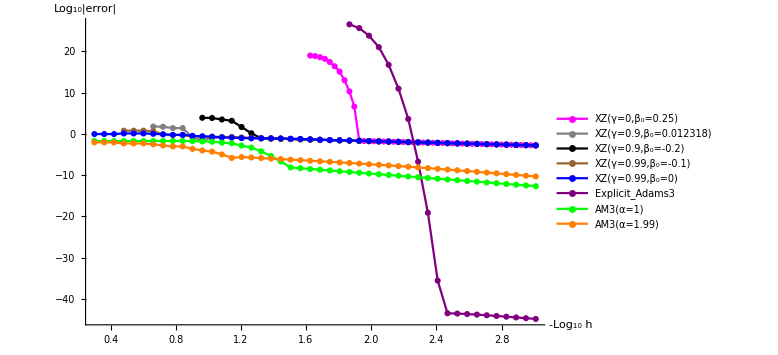

```mathematica
Show[p2,p12,p5,p6,p14,p1,p9,p11,PlotRange->Full,LabelStyle->{14,GrayLevel[0]},AxesLabel->{HoldForm[-Subscript[Log, 10](h)],HoldForm["Log_10|error| "]},ImageSize->Large,AxesOrigin->{0,0}]
```

OptionValue::nodef: Graphics 的未知选项 Image.

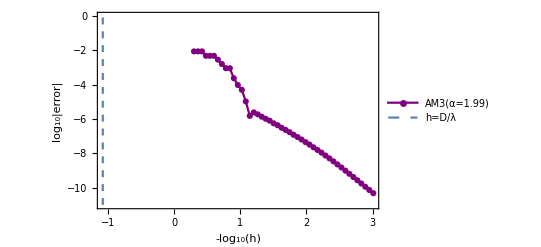

```mathematica
p11=ListLinePlot[data10,Joined->True,PlotStyle->Purple,PlotLegends->{"AM3(α=1.99)"},PlotMarkers->Automatic];
Show[p11,ParametricPlot[{-Log[10,11.94],t},{t,-11,0},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],Image->Large,LabelStyle->{15,GrayLevel[0]},Frame->True,FrameLabel->{"-log_10(h)","log_10|error| "},PlotRange->Full]
```